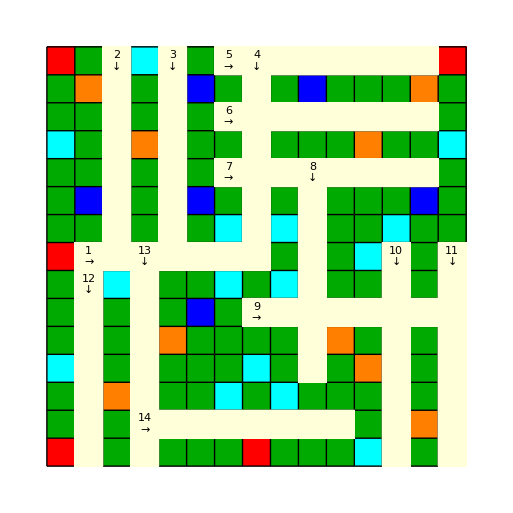
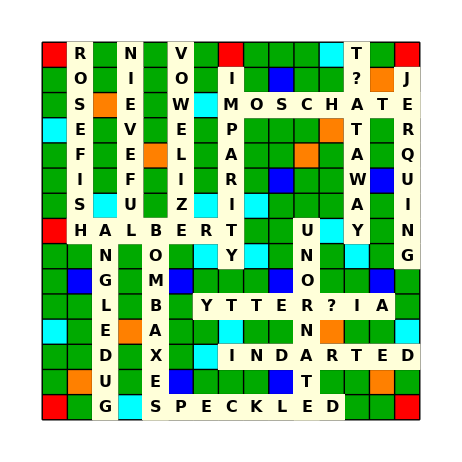
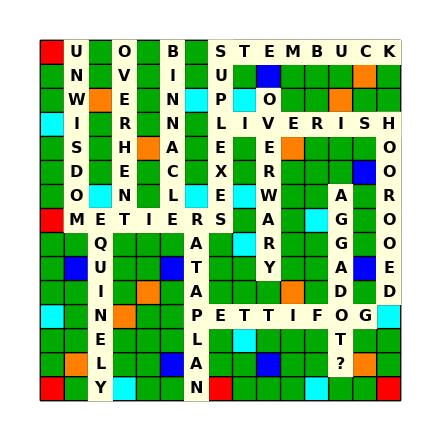

```mathematica
CanFormWord[tiles_,word_]:=AllTrue[
  Tally[Characters[word]],
  (Count[Characters[tiles],#[[1]]]>=#[[2]])&
]

Select[wordsByLength[8],CanFormWord["AAAAEFFGGIIIIJOOQVVXY",#]&]
```

{}

```mathematica
possibleWords={};
Do[
  Do[
    AppendTo[possibleWords,Echo@Select[wordsByLength[8],CanFormWord[StringJoin["ABEEMPZD",s1,s2],#]&]],
    {s1,ToUpperCase[Alphabet[]]}
  ],
  {s2,ToUpperCase[Alphabet[]]}
];
```

```mathematica
Sort[DeleteDuplicates[Flatten[possibleWords]]]
```

{ABAMPERE,BAPTIZED,BEADSMEN,BECALMED,BECAPPED,BEDAMNED,BEDAZZLE,BEDESMAN,BEDFRAME,BEDIAPER,BEDIMPLE,BEDLAMER,BEDLAMPS,BEDMAKER,BEDMATES,BEDPLATE,BEDRAPED,BEDRAPES,BEFOAMED,BELDAMES,BELEAPED,BEMADDED,BEMADDEN,BEMAULED,BEMEANED,BEMEDALS,BEMOANED,BEPATTED,BEPLUMED,BESHAMED,BESPREAD,BLAZERED,BRAZENED,BUMBAZED,BUMPERED,CAMBERED,DAMPENED,DAMPENER,DECAMPED,DIAZEPAM,EMBAILED,EMBALLED,EMBALMED,EMBANKED,EMBARKED,EMBARRED,EMBATHED,EMBLAZED,EMBLAZER,EMBLAZES,EMBRACED,EMBRAVED,EMBREADS,EMPAIRED,EMPARLED,EMPARTED,EMPAYRED,EMPLACED,EMPLANED,ENCAMPED,ENDAMEBA,ENJAMBED,EPENDYMA,EXAMPLED,EXCAMBED,FLAMBEED,GAZUMPED,HAMPERED,IMBLAZED,MADERIZE,MEGAPODE,MENDABLE,PAMPERED,PREAMBLE,PREARMED,PREBAKED,PREGAMED,REMAPPED,REVAMPED,SIAMEZED,SPADEMEN,SPREAZED,STAMPEDE,STEPDAME,TAMPERED,TRAPEZED}

### Visualize

```mathematica
assoc=<|1-><|"Bingo"->"BRASHED","Position"->{"H",2},"Direction"->"Right"|>,2-><|"Bingo"->"SPATTERS","Position"->{"A",5},"Direction"->"Down","Overlap"->"S"|>,3-><|"Bingo"->"AMOEBOID","Position"->{"H",4},"Direction"->"Down","Overlap"->"A"|>,4-><|"Bingo"->"UNCLOSED","Position"->{"A",8},"Direction"->"Down","Overlap"->"D"|>,5-><|"Bingo"->"DOWNCOME","Position"->{"O",4},"Direction"->"Right","Overlap"->"D"|>,6-><|"Bingo"->"EUTAXITE","Position"->{"G",8},"Direction"->"Right","Overlap"->"E"|>,7-><|"Bingo"->"ZOOPHORI","Position"->{"E",7},"Direction"->"Right","Overlap"->"O"|>,8-><|"Bingo"->"CRUSTILY","Position"->{"C",8},"Direction"->"Right","Overlap"->"C"|>,9-><|"Bingo"->"DEVELING","Position"->{"F",15},"Direction"->"Down","Overlap"->"E"|>,10-><|"Bingo"->"TINKERER","Position"->{"A",3},"Direction"->"Down","Overlap"->"R"|>,11-><|"Bingo"->"UNWIVING","Position"->{"A",8},"Direction"->"Right","Overlap"->"U"|>,12-><|"Bingo"->"OBLIQUER","Position"->{"L",3},"Direction"->"Right","Overlap"->"B"|>|>
```

<|1→<|Bingo→BRASHED,Position→{H,2},Direction→Right|>,2→<|Bingo→SPATTERS,Position→{A,5},Direction→Down,Overlap→S|>,3→<|Bingo→AMOEBOID,Position→{H,4},Direction→Down,Overlap→A|>,4→<|Bingo→UNCLOSED,Position→{A,8},Direction→Down,Overlap→D|>,5→<|Bingo→DOWNCOME,Position→{O,4},Direction→Right,Overlap→D|>,6→<|Bingo→EUTAXITE,Position→{G,8},Direction→Right,Overlap→E|>,7→<|Bingo→ZOOPHORI,Position→{E,7},Direction→Right,Overlap→O|>,8→<|Bingo→CRUSTILY,Position→{C,8},Direction→Right,Overlap→C|>,9→<|Bingo→DEVELING,Position→{F,15},Direction→Down,Overlap→E|>,10→<|Bingo→TINKERER,Position→{A,3},Direction→Down,Overlap→R|>,11→<|Bingo→UNWIVING,Position→{A,8},Direction→Right,Overlap→U|>,12→<|Bingo→OBLIQUER,Position→{L,3},Direction→Right,Overlap→B|>|>

```mathematica
epilogState={};

Do[
word=assoc[[i]]["Bingo"];
pos=assoc[[i]]["Position"];
dir=assoc[[i]]["Direction"];
epilogState=UpdateScrabbleBoard[word,pos,dir,epilogState];,
{i,Length[assoc]}
]
```

```mathematica
Iconize@epilogState
```

### Compare